```mathematica
(*ToDo: Comment on the below code, in particular, The If Statement above the While loop.
Andm comment on the structure of the Module;
	and, there's a link between this counting scheme, and the counting scheme for n!; derscribe it; describe how they are related..(this turned out not to be true, the number of ways to arrange n Items in m different ways is:= n^m, a closed form expression.)
On the other hand, it might be possible to come up with a different (not TOO different) counting scheme from the one explored here. 
It might be possible to come up with a closed-form expression to compute the cardinality of this counting scheme.
i suspect there may be a counting scheme which is more general than what is explored here. I suspect that the more general counting scheme reduces to this 
counting scheme, during a special case (some sort of zero-ing case)
*)




(*Note, the closed form expression is n^m *)
mArrangeN[listM_,sizeOfN_]:=Module[
{list :={},
listOmega:=listM
},
{
Recurse[current_]:=
Module[
{
currentAlpha=current,
iterator=1
},
{
(*Print[sizeOfN];*)
If[Length[currentAlpha]==sizeOfN,
{AppendTo[list,currentAlpha]
},(*Append the finished list to the list of lists...whose name is list....do not do the inside of the while in this case; skip it;l it's one or the other..*)
While[
iterator<Length[listOmega]+1, 

(*Print[iterator, Length[source]];*)
AppendTo[currentAlpha,listOmega[[iterator]]];
Recurse[currentAlpha];
currentAlpha = current;
iterator++
];
];
}
];

Recurse[{}];
list
}
]
```

```mathematica
result= mArrangeN[{0,1,2,3},3]
```

{{{0,0,0},{0,0,1},{0,0,2},{0,0,3},{0,1,0},{0,1,1},{0,1,2},{0,1,3},{0,2,0},{0,2,1},{0,2,2},{0,2,3},{0,3,0},{0,3,1},{0,3,2},{0,3,3},{1,0,0},{1,0,1},{1,0,2},{1,0,3},{1,1,0},{1,1,1},{1,1,2},{1,1,3},{1,2,0},{1,2,1},{1,2,2},{1,2,3},{1,3,0},{1,3,1},{1,3,2},{1,3,3},{2,0,0},{2,0,1},{2,0,2},{2,0,3},{2,1,0},{2,1,1},{2,1,2},{2,1,3},{2,2,0},{2,2,1},{2,2,2},{2,2,3},{2,3,0},{2,3,1},{2,3,2},{2,3,3},{3,0,0},{3,0,1},{3,0,2},{3,0,3},{3,1,0},{3,1,1},{3,1,2},{3,1,3},{3,2,0},{3,2,1},{3,2,2},{3,2,3},{3,3,0},{3,3,1},{3,3,2},{3,3,3}}}

```mathematica
Length[result[[1]]]
```

64

```mathematica
result= mArrangeN[{0,1,2,3,4},3]
```

{{{0,0,0},{0,0,1},{0,0,2},{0,0,3},{0,0,4},{0,1,0},{0,1,1},{0,1,2},{0,1,3},{0,1,4},{0,2,0},{0,2,1},{0,2,2},{0,2,3},{0,2,4},{0,3,0},{0,3,1},{0,3,2},{0,3,3},{0,3,4},{0,4,0},{0,4,1},{0,4,2},{0,4,3},{0,4,4},{1,0,0},{1,0,1},{1,0,2},{1,0,3},{1,0,4},{1,1,0},{1,1,1},{1,1,2},{1,1,3},{1,1,4},{1,2,0},{1,2,1},{1,2,2},{1,2,3},{1,2,4},{1,3,0},{1,3,1},{1,3,2},{1,3,3},{1,3,4},{1,4,0},{1,4,1},{1,4,2},{1,4,3},{1,4,4},{2,0,0},{2,0,1},{2,0,2},{2,0,3},{2,0,4},{2,1,0},{2,1,1},{2,1,2},{2,1,3},{2,1,4},{2,2,0},{2,2,1},{2,2,2},{2,2,3},{2,2,4},{2,3,0},{2,3,1},{2,3,2},{2,3,3},{2,3,4},{2,4,0},{2,4,1},{2,4,2},{2,4,3},{2,4,4},{3,0,0},{3,0,1},{3,0,2},{3,0,3},{3,0,4},{3,1,0},{3,1,1},{3,1,2},{3,1,3},{3,1,4},{3,2,0},{3,2,1},{3,2,2},{3,2,3},{3,2,4},{3,3,0},{3,3,1},{3,3,2},{3,3,3},{3,3,4},{3,4,0},{3,4,1},{3,4,2},{3,4,3},{3,4,4},{4,0,0},{4,0,1},{4,0,2},{4,0,3},{4,0,4},{4,1,0},{4,1,1},{4,1,2},{4,1,3},{4,1,4},{4,2,0},{4,2,1},{4,2,2},{4,2,3},{4,2,4},{4,3,0},{4,3,1},{4,3,2},{4,3,3},{4,3,4},{4,4,0},{4,4,1},{4,4,2},{4,4,3},{4,4,4}}}

```mathematica
Length@result[[1]]
```

125

```mathematica
(*

result = Table[{Table[i-1,{i,1,j}],j},{j,1,n}]

n is the number of things; in the context of n-ary lists, it is the number of entries in each list.
*)
```

```mathematica
n=5
result = Table[{Table[i-1,{i,1,j}],j},{j,1,n}]
```

5

{{{0},1},{{0,1},2},{{0,1,2},3},{{0,1,2,3},4},{{0,1,2,3,4},5}}

```mathematica
result[[1,1]]
result[[1,2]]
```

{0}

1

```mathematica
result[[2,1]]
result[[2,2]]
```

{0,1}

2

```mathematica
foo=Table[mArrangeN[result[[i,1]],result[[i,2]]],{i,1,5}]
```

{{{{0}}},3,{{{0,0,0,0,0},{0,0,0,0,1},{0,0,0,0,2},{0,0,0,0,3},{0,0,0,0,4},{0,0,0,1,0},{0,0,0,1,1},{0,0,0,1,2},{0,0,0,1,3},{0,0,0,1,4},{0,0,0,2,0},{0,0,0,2,1},{0,0,0,2,2},{0,0,0,2,3},{0,0,0,2,4},{0,0,0,3,0},{0,0,0,3,1},{0,0,0,3,2},{0,0,0,3,3},{0,0,0,3,4},{0,0,0,4,0},{0,0,0,4,1},{0,0,0,4,2},{0,0,0,4,3},{0,0,0,4,4},{0,0,1,0,0},{0,0,1,0,1},{0,0,1,0,2},{0,0,1,0,3},{0,0,1,0,4},{0,0,1,1,0},{0,0,1,1,1},{0,0,1,1,2},{0,0,1,1,3},{0,0,1,1,4},{0,0,1,2,0},{0,0,1,2,1},3051,{4,4,3,2,3},{4,4,3,2,4},{4,4,3,3,0},{4,4,3,3,1},{4,4,3,3,2},{4,4,3,3,3},{4,4,3,3,4},{4,4,3,4,0},{4,4,3,4,1},{4,4,3,4,2},{4,4,3,4,3},{4,4,3,4,4},{4,4,4,0,0},{4,4,4,0,1},{4,4,4,0,2},{4,4,4,0,3},{4,4,4,0,4},{4,4,4,1,0},{4,4,4,1,1},{4,4,4,1,2},{4,4,4,1,3},{4,4,4,1,4},{4,4,4,2,0},{4,4,4,2,1},{4,4,4,2,2},{4,4,4,2,3},{4,4,4,2,4},{4,4,4,3,0},{4,4,4,3,1},{4,4,4,3,2},{4,4,4,3,3},{4,4,4,3,4},{4,4,4,4,0},{4,4,4,4,1},{4,4,4,4,2},{4,4,4,4,3},{4,4,4,4,4}}}}
 |  |  |  |

```mathematica
foo=Table[Length[mArrangeN[result[[i,1]],result[[i,2]]][[1]]],{i,1,5}]
```

{1,4,27,256,3125}

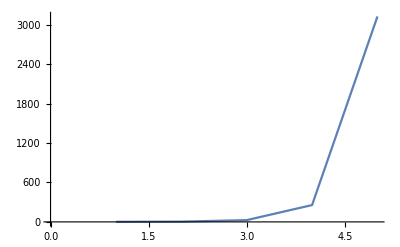

```mathematica
ListLinePlot@foo
```

```mathematica
n=10
result = Table[{Table[i-1,{i,1,j}],j},{j,1,n}]
foo=Table[Length[mArrangeN[result[[i,1]],result[[i,2]]][[1]]],{i,1,n}]
```

10

{{{0},1},{{0,1},2},{{0,1,2},3},{{0,1,2,3},4},{{0,1,2,3,4},5},{{0,1,2,3,4,5},6},{{0,1,2,3,4,5,6},7},{{0,1,2,3,4,5,6,7},8},{{0,1,2,3,4,5,6,7,8},9},{{0,1,2,3,4,5,6,7,8,9},10}}

```mathematica
ListLinePlot@foo
```

-Graphics-